```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2"]
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
viewpoint={-1.785849751660347,-2.7180538166735624,0.9343040801371536}
```

{-1.78585,-2.71805,0.934304}

```mathematica
dir="mc1e6_1sym_1snp_conserv\\";
filesamples="freq-1_1_conserv-";
```

```mathematica
mcmc=Import[dir<>filesamples<>"priorsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mcmc]
```

{1000000,2}

```mathematica
mpari=Exp@mcmc;
```

```mathematica
bd[f_,u_,v_]=Assuming[u>0&&v>0&&0<f<1,FS[PDF[BetaDistribution[v,u],f]]]
```

((1-f)^(-1+u) f^(-1+v))/Beta[v,u]

```mathematica
fbeta[f1_,f2_]=With[{samps=mpari[[;;;;10]]},Sum[bd[f1,Sequence@@pars]*bd[f2,Sequence@@pars]/Length@samps,{pars,samps}]];
```

```mathematica
fbeta[0.5,0.5]
```

13.9352

```mathematica
fbeta[0.4,0.6]
```

0.0449808

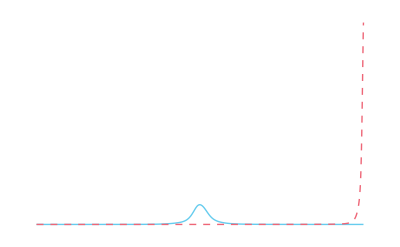

```mathematica
Plot[{fbeta[0.5,f],fbeta[0.99,f]},{f,0.01,0.99},PlotRange->All]
```

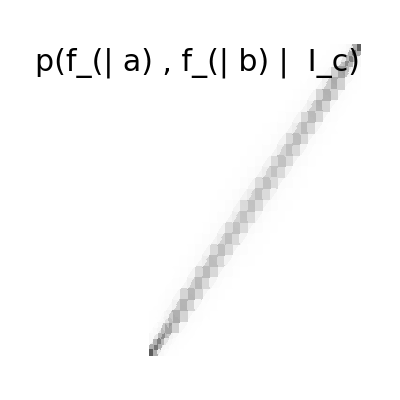

```mathematica
plot=DensityPlot[fbeta[f1,f2],{f1,0.025,0.975},{f2,0.025,0.975},PlotRange->{{0,1},{0,1},{0,All}},ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),AspectRatio->1,ImageSize->a5rsize[[1]],FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"c"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["conserv_prior_dens2.png",Style[plot,Magnification->1],ImageResolution->300]
```

conserv_prior_dens2.png

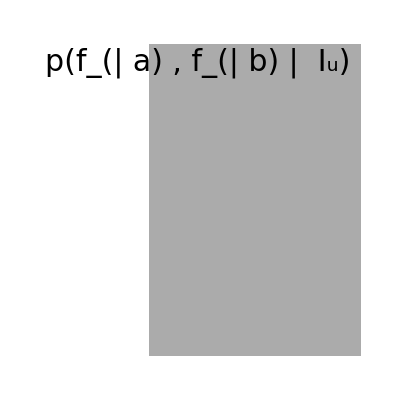

```mathematica
plot2=DensityPlot[0.33,{f1,0.025,0.975},{f2,0.025,0.975},PlotRange->{{0,1},{0,1},{0,All}},ColorFunctionScaling->False,ColorFunction->(GrayLevel[1-#]&),AspectRatio->1,ImageSize->a5rsize[[1]],FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"u"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["unif_prior_dens2.png",Style[plot2,Magnification->1],ImageResolution->300]
```

unif_prior_dens2.png

```mathematica
mcmc=Import[dir<>filesamples<>"priorsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mcmc]
```

{1000000,2}

```mathematica
mpari=Exp@mcmc;
```

```mathematica
Mean[mpari]
```

{500.842,500.731}

```mathematica
Mean[mcmc]
```

{5.33149,5.33081}

```mathematica
Exp@%
```

{206.745,206.604}

```mathematica
Median[mpari]
```

{267.534,267.575}

```mathematica
Median[mcmc]
```

{5.58925,5.5894}

```mathematica
Exp@%
```

{267.534,267.575}

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
ClearAll[fbeta,mcmc];
```

```mathematica
samplesi=Import[dir<>filesamples<>"priorfsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[samplesi]
```

{1000000,2}

```mathematica
samplesi=Cases[samplesi(*[[;;;;Round[Length[samplesi]/100000]]]*),{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[samplesi]
```

999497

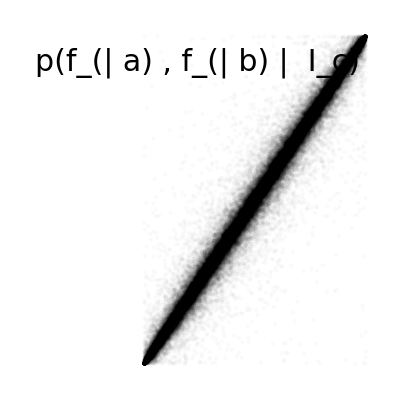

```mathematica
plot=ListPlot[samplesi[[;;;;10]],Joined->False,PlotStyle->{Opacity[0.02],PointSize[Small],Black},PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->a5rsize[[1]],FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"c"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["conserv_prior_list.png",Style[plot,Magnification->1],ImageResolution->300]
```

conserv_prior_list.png

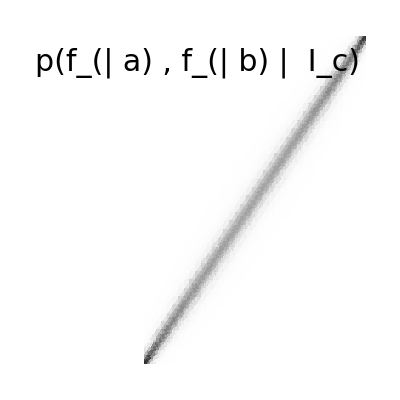

```mathematica
plot=SmoothDensityHistogram[samplesi,"LeastSquaresCrossValidation","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[1-#]&),Mesh->None,MeshStyle->Directive[red],ImageSize->a5rsize[[1]],PlotRange->{{0,1},{0,1}},FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"c"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["conserv_prior_dens.png",Style[plot,Magnification->1],ImageSize->a5rsize[[1]],ImageResolution->400]
```

conserv_prior_dens.png

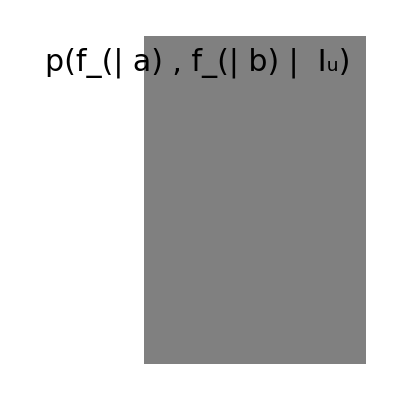

```mathematica
plot=SmoothDensityHistogram[samplesi[[;;;;1000]],"LeastSquaresCrossValidation","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[0.5]&),Mesh->None,MeshStyle->Directive[red],ImageSize->a5rsize[[1]],PlotRange->{{0,1},{0,1}},(*
FrameTicksStyle->Directive[Large,FontSize->21],
FrameStyle->Directive[Black,myfontsize,FontFamily->Auto],*)FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"u"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["unif_prior_dens.png",Style[plot,Magnification->1],ImageSize->a5rsize[[1]],ImageResolution->400]
```

unif_prior_dens.png

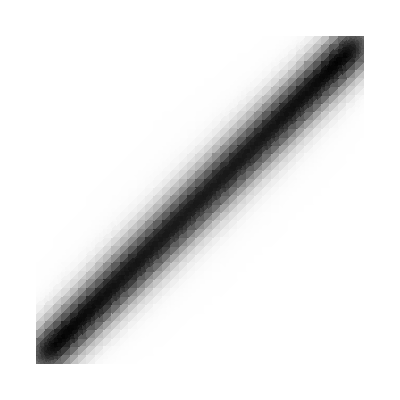

```mathematica
SmoothDensityHistogram[samplesi,"Scott","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[1-#]&),Mesh->None,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
SmoothDensityHistogram[samplesi,"SheatherJones","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[1-#]&),Mesh->None,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

SmoothDensityHistogram[samplesi,SheatherJones,PDF,ColorFunctionScaling→True,ColorFunction→(GrayLevel[1-#1]&),Mesh→None,MeshStyle→Directive[RGBColor[Rational[14, 15], Rational[2, 5], Rational[7, 15]]],PlotRange→{{0,1},{0,1}}]

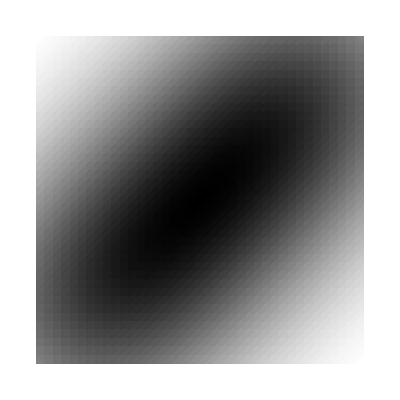

```mathematica
SmoothDensityHistogram[samplesi,"StandardDeviation","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[1-#]&),Mesh->None,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

```mathematica
SmoothDensityHistogram[samplesi,"StandardGaussian","PDF",ColorFunctionScaling->True,ColorFunction->(*mycolorfunction[#,-1]&*)(GrayLevel[1-#]&),Mesh->None,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

-Graphics-

```mathematica
viewpoint={-1.785849751660347,-2.7180538166735624,0.9343040801371536}
```

{-1.78585,-2.71805,0.934304}

```mathematica
plot=SmoothHistogram3D[samplesi(*[[;;;;1000]]*),"LeastSquaresCrossValidation","PDF",Mesh->5,ColorFunction->Function[{x,y,z},GrayLevel[1-z]],MeshStyle->red,PlotRange->{{0,1},{0,1},{0,All}},Axes->True,
ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},
ImageSize->a5rsize[[1]]*1.25,
AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate[

"p"[HoldForm[Subscript[f,s"|"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"c"] ]]

,Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["conserv3_prior.png",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
plot=Plot3D[0.5,{x,0,1},{y,0,1},Mesh->None,ColorFunction->Function[{x,y,z},GrayLevel[1-0.5]],MeshStyle->red,PlotRange->{{0,1},{0,1},{0,1}},Axes->True,
ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},
ImageSize->a5rsize[[1]]*1.25,
AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate[

"p"[HoldForm[Subscript[f,s"|"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"u"] ]]

,Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["const_prior.png",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
(* cauchy prior *)
```

```mathematica
dir="testmc1e6_1sym_1snp_cauchy\\";
filesamples="freq-1_1_cauchy-";
```

```mathematica
mcmc=Import[dir<>filesamples<>"priorsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mcmc]
```

{1000000,2}

```mathematica
mpari=Exp@mcmc;
```

```mathematica
mpari=Import[dir<>filesamples<>"priorfsamples.csv"][[2;;,2;;]];
```

```mathematica
Dimensions[mpari]
```

{1000000,2}

```mathematica
samplesi=mpari;
```

```mathematica
samplesi={RandomVariate[BetaDistribution[Sequence@@#]],RandomVariate[BetaDistribution[Sequence@@#]]}&/@mpari;
```

```mathematica
samplesi=Cases[samplesi[[;;;;Round[Length[samplesi]/100000]]],{_?MachineNumberQ,_?MachineNumberQ}];
```

```mathematica
Length[samplesi]
```

70390

```mathematica
SmoothDensityHistogram[samplesi,"Oversmooth","PDF",ColorFunctionScaling->True,ColorFunction->(GrayLevel[1-#]&),Mesh->5,MeshStyle->Directive[red],PlotRange->{{0,1},{0,1}}]
```

$Aborted

```mathematica
plot=SmoothHistogram3D[samplesi,Auto,"PDF",Mesh->5,ColorFunction->Function[{x,y,z},GrayLevel[1-z]],MeshStyle->red,PlotRange->{{0,1},{0,1},{0,All}},Axes->True,
ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},
ImageSize->a5rsize[[1]]*1.25,
AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate[

"p"[HoldForm[Subscript[f,s"|"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"c"] ]]

,Pi/2,{-2,0}]}]
```

-Graphics3D-

```mathematica
Export["cauchy_prior.png",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
Histogram3D[samplesi[[;;;;100]],50,"PDF",ColorFunction->Function[z,GrayLevel[1-z]],PlotRange->{{0,1},{0,1},{0,All}},Axes->True,ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},Axes->Auto,Lighting->Auto,AxesLabel->{Subscript[f,HoldForm[s"|"a]],Subscript[f,HoldForm[s"|"b]],Rotate["p"[HoldForm[Subscript[f,s" |"a]","Subscript[f,s"|"b]"| "Subscript[Style["I",Italic],"g"] ]],Pi/2,{1.25,0}]}]
```

-Graphics3D-

```mathematica
samplesu=T@{RandomVariate[UniformDistribution[],Length@samplesi],RandomVariate[UniformDistribution[],Length@samplesi]};
```

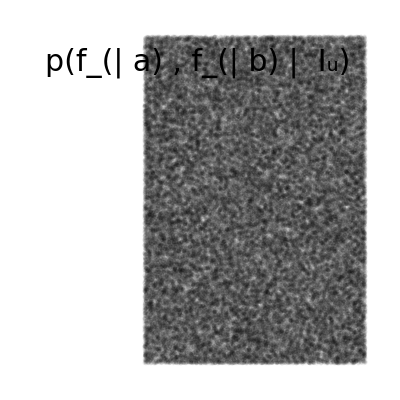

```mathematica
plot=ListPlot[samplesu[[;;;;10]],Joined->False,PlotStyle->{Opacity[0.05],PointSize[Small],Black},PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->a5rsize[[1]],FrameLabel->{Style[Subscript[f,HoldForm["|"a]],33],Style[Subscript[f,HoldForm["|"b]],33]},
Epilog->Text[Style["p"[HoldForm[Subscript[f,"|"a]","Subscript[f,"|"b]"| "Subscript[Style["I",Italic],"u"]]] ,30],Sequence@@labelposition[{0.25,0.95}]]]
```

```mathematica
Export["unif_prior_list.png",Style[plot,Magnification->1],ImageResolution->300]
```

unif_prior_list.png